## Using PRIMAT. Abundances and plots

### Loading PRIMAT

Setting the notebook directory (in batch mode this is not evaluated because it seems to be the default one)

```mathematica
SetDirectory[NotebookDirectory[]];
```

Then we go the parent directory, or base directory of PRIMAT.

```mathematica
SetDirectory[ParentDirectory[Directory[]]]
```

/Users/pitrou/Dropbox/iap/notebooks/BBN

We load PRIMAT. It takes some time because it starts reading the file with nuclear reactions and deduces which are the nuclides needed, 
and it starts to build formally the network of equations

```mathematica
Timing[<<PRIMAT-Main.m]
```

{16.8608,Null}

### Integration and results

```mathematica
Timing[RunNumericalIntegrals]
```

{48.8079,Null}

Main species of the small network

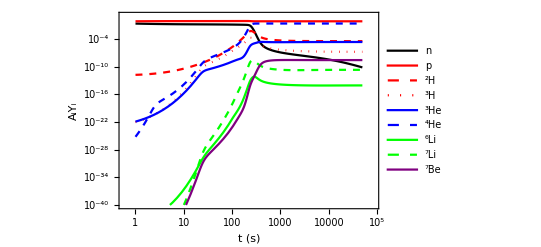

```mathematica
LogLogPlot[{YI["n"][tv],YI["p"][tv],2YI["d"][tv],3YI["t"][tv],3YI["He3"][tv],4YI["a"][tv],YI["Li6"][tv],YI["Li7"][tv],7YI["Be7"][tv]},{tv,tmiddle,tend},Frame->True,FrameLabel->{"t (s)","A_iY_i"},LabelStyle->{FontSize->12},PlotRange->{10^-40,10},PlotStyle->{Black,Red,{Red,Dashed},{Red,Dotted},Blue,{Blue,Dashed},Green,{Green,Dashed},Purple},ImagePadding->{{50,10},{40,25}},PlotLegends->Placed[LineLegend[{"n","p","^2H","^3H","^3He","^4He","^6Li","^7Li","^7Be"},LegendLayout->(Grid[#,Frame->None]&)],Right]]
```

From Hydrogen to Borron

```mathematica
ListColor[Color_,n_]:=Take[Join[{{Color,Thickness[0.004]}},
Table[{Color,Thickness[0.004],Dashing[(i)0.01]},{i,1,3}],
Table[{Color,Thickness[0.004],Dashing[{0,0.015*i,(i)0.015,i 0.015}]},{i,1,4}]],n]
```

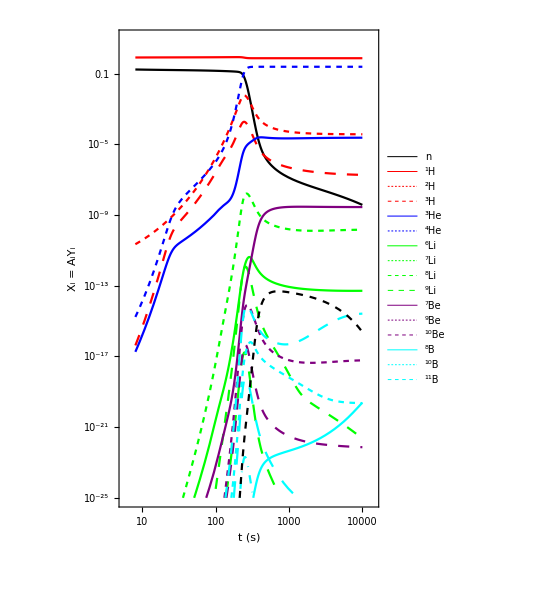

```mathematica
LogLogPlot[{XI["n"][tv],XI["p"][tv],XI["d"][tv],XI["t"][tv],XI["He3"][tv],XI["a"][tv],XI["Li6"][tv],XI["Li7"][tv],XI["Li8"][tv],XI["Li9"][tv],XI["Be7"][tv],XI["Be9"][tv],XI["Be10"][tv],XI["B8"][tv],XI["B10"][tv],XI["B11"][tv],XI["B12"][tv],XI["B13"][tv],XI["C11"][tv]},{tv,8,10^4},Frame->True,FrameLabel->{"t (s)","X_i = A_iY_i"},LabelStyle->{FontSize->12},FrameStyle->Thickness[0.004],PlotRange->{10^-25,9},PlotStyle->Join[ListColor[Black,1],ListColor[Red,3],ListColor[Blue,2],ListColor[Green,4],ListColor[Purple,3],ListColor[Cyan,5],{{Black,Thickness[0.004],Dashed}}],AspectRatio->1.5,FrameTicks->MyTickst,ImagePadding->{{50,10},{40,25}},PlotLegends->Placed[LineLegend[{"n","^1H","^2H","^3H","^3He","^4He","^6Li","^7Li","^8Li","^9Li","^7Be","^9Be","^10Be","^8B","^10B","^11B","^12B","^13B","^11C"},LegendLayout->(Grid[#,Frame->None]&)],Right]]
```

From Carbon to Oxygen

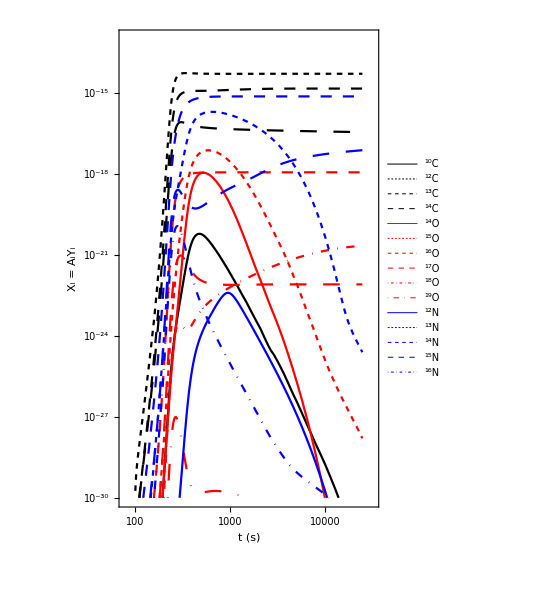

```mathematica
LogLogPlot[{XI["C10"][tv],XI["C12"][tv],XI["C13"][tv],XI["C14"][tv],XI["O14"][tv],XI["O15"][tv],XI["O16"][tv],XI["O17"][tv],XI["O18"][tv],XI["O19"][tv],XI["N12"][tv],XI["N13"][tv],XI["N14"][tv],XI["N15"][tv],XI["N16"][tv]},{tv,1.01t18,tend/2},Frame->True,FrameLabel->{"t (s)","X_i = A_iY_i"},LabelStyle->{FontSize->12},FrameStyle->Thickness[0.004],PlotRange->{10^-30,10^-13},PlotStyle->Join[ListColor[Black,4],ListColor[Red,6],ListColor[Blue,5],ListColor[Purple,1]],AspectRatio->1.5,FrameTicks->MyTickst,ImagePadding->{{50,10},{40,25}},PlotLegends->Placed[LineLegend[{"^10C","^12C","^13C","^14C","^14O","^15O","^16O","^17O","^18O","^19O","^12N","^13N","^14N","^15N","^16N"},LegendLayout->(Grid[#,Frame->None]&)],Right]]
```

Standard abundances as reported in most BBN papers.  Note the definition Y_P = 4 Y_He4. Since the atomic mass of Helium is not exactly 4 this is not exactly Helium mass abundance

```mathematica
MyGrid@Transpose[{{"H","Y_P=4Y_He","D/H x10^5","^3He/H x10^5","T/H x10^8","(^3He+T)/H x10^5","^7Li/H x10^11","^7Be/H x10^10","(^7Li+^7Be)/H x10^10","^6Li/H x10^14","^9Be/H x10^19","^10B/H x10^21","^11B/H x10^16","CNO/H x10^16"},{Yf["p"],4Yf["a"],YfH["d"] 10^5,YfH["He3"] 10^5,YfH["t"] 10^8,(YfH["t"]+YfH["He3"])10^5,YfH["Li7"] 10^11,YfH["Be7"] 10^10,(YfH["Li7"]+YfH["Be7"])10^10,YfH["Li6"] 10^14,YfH["Be9"] 10^19,YfH["B10"] 10^21,YfH["B11"] 10^16,YfH["CNO"] 10^16}}]
```

H | 0.752702
Y_P=4Y_He | 0.247237
D/H x10^5 | 2.46002
^3He/H x10^5 | 1.06622
T/H x10^8 | 7.96465
(^3He+T)/H x10^5 | 1.07418
^7Li/H x10^11 | 2.89192
^7Be/H x10^10 | 5.38317
(^7Li+^7Be)/H x10^10 | 5.67236
^6Li/H x10^14 | 1.19358
^9Be/H x10^19 | 9.20396
^10B/H x10^21 | 2.99636
^11B/H x10^16 | 3.27561
CNO/H x10^16 | 8.04592

All abundances

```mathematica
MyGrid[{#,Yf[#]}&/@ShortNames]
```

n | 7.2938×10^-11
p | 0.752702
d | 0.0000185166
t | 5.99501×10^-8
He3 | 8.02543×10^-6
a | 0.0618092
He6 | 4.59922×10^-44
Li6 | 8.98413×10^-15
Li7 | 2.17675×10^-11
Li8 | 5.13204×10^-26
Li9 | 3.44787×10^-41
Be7 | 4.05192×10^-10
Be9 | 6.92784×10^-19
Be10 | 6.78271×10^-24
Be11 | 2.60853×10^-38
Be12 | 1.11336×10^-55
B8 | 1.05174×10^-23
B10 | 2.25536×10^-21
B11 | 2.46556×10^-16
B12 | 1.83681×10^-32
B13 | 1.68713×10^-48
B14 | 2.74376×10^-63
B15 | 1.56175×10^-81
C9 | 2.08443×10^-40
C10 | 1.13194×10^-36
C11 | 4.68362×10^-27
C12 | 4.35033×10^-16
C13 | 1.13501×10^-16
C14 | 2.46672×10^-18
C15 | 5.47926×10^-34
C16 | 2.09661×10^-49
N12 | 1.54735×10^-45
N13 | 1.48927×10^-28
N14 | 5.3943×10^-17
N15 | 6.0132×10^-19
N16 | 3.27201×10^-34
N17 | 2.6157×10^-44
O13 | -1.07497×10^-58
O14 | 3.27483×10^-43
O15 | 6.64691×10^-32
O16 | 7.25573×10^-20
O17 | 4.79619×10^-24
O18 | 1.32861×10^-22
O19 | 6.7166×10^-36
O20 | 6.41886×10^-49
F17 | 5.55314×10^-36
F18 | 8.64138×10^-25
F19 | 6.31251×10^-26
F20 | 3.86974×10^-38
Ne18 | 3.76277×10^-49
Ne19 | 1.29265×10^-41
Ne20 | 6.8384×10^-28
Ne21 | 5.34083×10^-30
Ne22 | 8.84848×10^-32
Ne23 | -2.95729×10^-74
Na20 | 8.38535×10^-64
Na21 | -7.76309×10^-78
Na22 | 1.72932×10^-36
Na23 | 1.08706×10^-37

### Information on rates

```mathematica
MyGrid[Join[{{"Reaction Name","Initial species","Final Species","Uncertainty","Reference"}},NiceDisplayReaction/@ListReactionsUpToChosenMass]]
```

Reaction Name | Initial species | Final Species | Uncertainty | Reference | 
n -> p | {n} | {p} | 0 | Companion Paper | 
np -> dg | {n,p} | {d,g} | 0 | And06 | 
dp -> He3g | {d,p} | {He3,g} | 0 | Ili16 | 
dd -> He3n | {d,d} | {He3,n} | 0 | Gom17 | 
dd -> tp | {d,d} | {t,p} | 0 | Gom17 | 
tp -> ag | {t,p} | {a,g} | 0 | Ser04 | 
td -> an | {t,d} | {a,n} | 0 | DAACV04 | 
ta -> Li7g | {t,a} | {Li7,g} | 0 | DAACV04 | 
He3n -> tp | {He3,n} | {t,p} | 0 | DAACV04 | 
He3d -> ap | {He3,d} | {a,p} | 0 | DAACV04 | 
He3a -> Be7g | {He3,a} | {Be7,g} | 0 | Ili16 | 
Be7n -> Li7p | {Be7,n} | {Li7,p} | 0 | DAACV04 | 
Li7p -> aa | {Li7,p} | {a,a} | 0 | DAACV04 | 
Li7p -> aag | {Li7,p} | {a,a,g} | 0 | NACRE | 
Be7n -> aa | {Be7,n} | {a,a} | 0 | Bar16 | 
da -> Li6g | {d,a} | {Li6,g} | 0 | Ham10 | 
Li6p -> Be7g | {Li6,p} | {Be7,g} | 0 | NACRE | 
Li6p -> He3a | {Li6,p} | {He3,a} | 0 | NACRE | 
Be9t -> B11n | {Be9,t} | {B11,n} | 0 | TALYS2 | 
O18n -> O19g | {O18,n} | {O19,g} | 0 | TALYS2 | 
Li9p -> He6a | {Li9,p} | {He6,a} | 0 | =li7pa!! | 
Li9d -> Be10n | {Li9,d} | {Be10,n} | 0 | TALYS2 | 
Be10a -> C14g | {Be10,a} | {C14,g} | 0 | TALYS2 | 
N12n -> C12p | {N12,n} | {C12,p} | 0 | TALYS2 | 
Li9p -> Be9n | {Li9,p} | {Be9,n} | 0 | TALYS2 | 
Li9a -> B12n | {Li9,a} | {B12,n} | 0 | New2011 | 
Li9p -> Be10g | {Li9,p} | {Be10,g} | 0 | TALYS2 | 
N13n -> N14g | {N13,n} | {N14,g} | 0 | TALYS2 | 
B10a -> N14g | {B10,a} | {N14,g} | 0 | TALYS2 | 
B8a -> N12g | {B8,a} | {N12,g} | 0 | TALYS2 | 
B12p -> Be9a | {B12,p} | {Be9,a} | 0 | TALYS2 | 
Be10p -> B11g | {Be10,p} | {B11,g} | 0 | TALYS2 | 
Be10p -> Li7a | {Be10,p} | {Li7,a} | 0 | TALYS2 | 
Be11p -> Li8a | {Be11,p} | {Li8,a} | 0 | TALYS2 | 
Be11p -> B11n | {Be11,p} | {B11,n} | 0 | TALYS2 | 
B8n -> aap | {B8,n} | {a,a,p} | 0 | TALYS2 | 
B10n -> B11g | {B10,n} | {B11,g} | 0 | TALYS2 | 
B10a -> C13p | {B10,a} | {C13,p} | 0 | TALYS2 | 
O17n -> O18g | {O17,n} | {O18,g} | 0 | TALYS2 | 
F17n -> O17p | {F17,n} | {O17,p} | 0 | TALYS2 | 
F18n -> O18p | {F18,n} | {O18,p} | 0 | TALYS2 | 
Be10a -> C13n | {Be10,a} | {C13,n} | 0 | TALYS2 | 
Be11a -> C14n | {Be11,a} | {C14,n} | 0 | TALYS2 | 
N14a -> F18g | {N14,a} | {F18,g} | 0 | ILCCF10 | 
N15a -> F19g | {N15,a} | {F19,g} | 0 | ILCCF10 | 
O15a -> Ne19g | {O15,a} | {Ne19,g} | 0 | ILCCF10 | 
O16p -> F17g | {O16,p} | {F17,g} | 0 | ILCCF10 | 
O16a -> Ne20g | {O16,a} | {Ne20,g} | 0 | ILCCF10 | 
O17p -> F18g | {O17,p} | {F18,g} | 0 | ILCCF10 | 
O18p -> F19g | {O18,p} | {F19,g} | 0 | ILCCF10 | 
O18a -> Ne22g | {O18,a} | {Ne22,g} | 0 | ILCCF10 | 
F17p -> Ne18g | {F17,p} | {Ne18,g} | 0 | ILCCF10 | 
F18p -> Ne19g | {F18,p} | {Ne19,g} | 0 | ILCCF10 | 
Ne19p -> Na20g | {Ne19,p} | {Na20,g} | 0 | ILCCF10 | 
O17p -> N14a | {O17,p} | {N14,a} | 0 | ILCCF10 | 
O18p -> N15a | {O18,p} | {N15,a} | 0 | ILCCF10 | 
F18p -> O15a | {F18,p} | {O15,a} | 0 | ILCCF10 | 
C14a -> O18g | {C14,a} | {O18,g} | 0 | ILCCF10 | 
C14p -> N15g | {C14,p} | {N15,g} | 0 | ILCCF10 | 
Be12p -> Li9a | {Be12,p} | {Li9,a} | 0 | TALYS2 | 
Li6He3 -> aap | {Li6,He3} | {a,a,p} | 0 | TALYS2 | 
Li6t -> Be9g | {Li6,t} | {Be9,g} | 0 | TALYS2 | 
Li6t -> aan | {Li6,t} | {a,a,n} | 0 | TALYS2 | 
Li6t -> Li8p | {Li6,t} | {Li8,p} | 0 | TALYS2 | 
Li7d -> Be9g | {Li7,d} | {Be9,g} | 0 | New2011 | 
Li7He3 -> B10g | {Li7,He3} | {B10,g} | 0 | TALYS2 | 
Li7He3 -> Li6a | {Li7,He3} | {Li6,a} | 0 | TALYS2 | 
Li7t -> Be10g | {Li7,t} | {Be10,g} | 0 | TALYS2 | 
Li8a -> B12g | {Li8,a} | {B12,g} | 0 | TALYS2 | 
Li8a -> B11n | {Li8,a} | {B11,n} | 0 | New2011 | 
Li8d -> Be10g | {Li8,d} | {Be10,g} | 0 | TALYS2 | 
Li8He3 -> B11g | {Li8,He3} | {B11,g} | 0 | TALYS2 | 
Li8He3 -> B10n | {Li8,He3} | {B10,n} | 0 | TALYS2 | 
Li8He3 -> Be10p | {Li8,He3} | {Be10,p} | 0 | TALYS2 | 
Li8He3 -> Li7a | {Li8,He3} | {Li7,a} | 0 | TALYS2 | 
Li8t -> Be11g | {Li8,t} | {Be11,g} | 0 | TALYS2 | 
Li8t -> Be10n | {Li8,t} | {Be10,n} | 0 | TALYS2 | 
Li9a -> B13g | {Li9,a} | {B13,g} | 0 | TALYS2 | 
Li9d -> Be11g | {Li9,d} | {Be11,g} | 0 | TALYS2 | 
Li9He3 -> B12g | {Li9,He3} | {B12,g} | 0 | TALYS2 | 
Li9He3 -> B11n | {Li9,He3} | {B11,n} | 0 | TALYS2 | 
Li9He3 -> Be11p | {Li9,He3} | {Be11,p} | 0 | TALYS2 | 
Li9He3 -> Li8a | {Li9,He3} | {Li8,a} | 0 | TALYS2 | 
Li9t -> Be12g | {Li9,t} | {Be12,g} | 0 | TALYS2 | 
Li9t -> Be11n | {Li9,t} | {Be11,n} | 0 | TALYS2 | 
Be7He3 -> C10g | {Be7,He3} | {C10,g} | 0 | TALYS2 | 
Be7t -> B10g | {Be7,t} | {B10,g} | 0 | TALYS2 | 
Be7t -> Be9p | {Be7,t} | {Be9,p} | 0 | New2011 | 
Be7t -> Li6a | {Be7,t} | {Li6,a} | 0 | TALYS2 | 
Be9a -> C13g | {Be9,a} | {C13,g} | 0 | TALYS2 | 
Be9d -> B11g | {Be9,d} | {B11,g} | 0 | TALYS2 | 
Be9d -> B10n | {Be9,d} | {B10,n} | 0 | TALYS2 | 
Be9d -> Be10p | {Be9,d} | {Be10,p} | 0 | TALYS2 | 
Be9d -> Li7a | {Be9,d} | {Li7,a} | 0 | TALYS2 | 
Be9He3 -> C12g | {Be9,He3} | {C12,g} | 0 | TALYS2 | 
Be9He3 -> C11n | {Be9,He3} | {C11,n} | 0 | TALYS2 | 
Be9He3 -> B11p | {Be9,He3} | {B11,p} | 0 | TALYS2 | 
Be9He3 -> aaa | {Be9,He3} | {a,a,a} | 0 | TALYS2 | 
Be9t -> B12g | {Be9,t} | {B12,g} | 0 | TALYS2 | 
Be9t -> Li8a | {Be9,t} | {Li8,a} | 0 | TALYS2 | 
Be10d -> B12g | {Be10,d} | {B12,g} | 0 | TALYS2 | 
Be10d -> B11n | {Be10,d} | {B11,n} | 0 | TALYS2 | 
Be10d -> Li8a | {Be10,d} | {Li8,a} | 0 | TALYS2 | 
Be10He3 -> C13g | {Be10,He3} | {C13,g} | 0 | TALYS2 | 
Be10He3 -> C12n | {Be10,He3} | {C12,n} | 0 | TALYS2 | 
Be10He3 -> B12p | {Be10,He3} | {B12,p} | 0 | TALYS2 | 
Be10He3 -> Be9a | {Be10,He3} | {Be9,a} | 0 | TALYS2 | 
Be10t -> B13g | {Be10,t} | {B13,g} | 0 | TALYS2 | 
Be10t -> B12n | {Be10,t} | {B12,n} | 0 | TALYS2 | 
Be10t -> Li9a | {Be10,t} | {Li9,a} | 0 | TALYS2 | 
Be11a -> C15g | {Be11,a} | {C15,g} | 0 | TALYS2 | 
Be11d -> B13g | {Be11,d} | {B13,g} | 0 | TALYS2 | 
Be11d -> B12n | {Be11,d} | {B12,n} | 0 | TALYS2 | 
Be11d -> Be12p | {Be11,d} | {Be12,p} | 0 | TALYS2 | 
Be11d -> Li9a | {Be11,d} | {Li9,a} | 0 | TALYS2 | 
Be11He3 -> C14g | {Be11,He3} | {C14,g} | 0 | TALYS2 | 
Be11He3 -> C13n | {Be11,He3} | {C13,n} | 0 | TALYS2 | 
Be11He3 -> B13p | {Be11,He3} | {B13,p} | 0 | TALYS2 | 
Be11He3 -> Be10a | {Be11,He3} | {Be10,a} | 0 | TALYS2 | 
Be11p -> B12g | {Be11,p} | {B12,g} | 0 | TALYS2 | 
Be11t -> B14g | {Be11,t} | {B14,g} | 0 | TALYS2 | 
Be11t -> B13n | {Be11,t} | {B13,n} | 0 | TALYS2 | 
Be12a -> C16g | {Be12,a} | {C16,g} | 0 | TALYS2 | 
Be12a -> C15n | {Be12,a} | {C15,n} | 0 | TALYS2 | 
Be12d -> B14g | {Be12,d} | {B14,g} | 0 | TALYS2 | 
Be12d -> B13n | {Be12,d} | {B13,n} | 0 | TALYS2 | 
Be12He3 -> C15g | {Be12,He3} | {C15,g} | 0 | TALYS2 | 
Be12He3 -> C14n | {Be12,He3} | {C14,n} | 0 | TALYS2 | 
Be12He3 -> B14p | {Be12,He3} | {B14,p} | 0 | TALYS2 | 
Be12He3 -> Be11a | {Be12,He3} | {Be11,a} | 0 | TALYS2 | 
Be12p -> B13g | {Be12,p} | {B13,g} | 0 | TALYS2 | 
Be12p -> B12n | {Be12,p} | {B12,n} | 0 | TALYS2 | 
Be12t -> B15g | {Be12,t} | {B15,g} | 0 | TALYS2 | 
Be12t -> B14n | {Be12,t} | {B14,n} | 0 | TALYS2 | 
B8a -> C11p | {B8,a} | {C11,p} | 0 | TALYS2 | 
B8d -> C10g | {B8,d} | {C10,g} | 0 | TALYS2 | 
B8He3 -> C10p | {B8,He3} | {C10,p} | 0 | TALYS2 | 
B8t -> C11g | {B8,t} | {C11,g} | 0 | TALYS2 | 
B8t -> C10n | {B8,t} | {C10,n} | 0 | TALYS2 | 
B8t -> B10p | {B8,t} | {B10,p} | 0 | TALYS2 | 
B8t -> Be7a | {B8,t} | {Be7,a} | 0 | TALYS2 | 
B10d -> C12g | {B10,d} | {C12,g} | 0 | TALYS2 | 
B10d -> C11n | {B10,d} | {C11,n} | 0 | TALYS2 | 
B10d -> B11p | {B10,d} | {B11,p} | 0 | TALYS2 | 
B10d -> aaa | {B10,d} | {a,a,a} | 0 | TALYS2 | 
B10He3 -> N13g | {B10,He3} | {N13,g} | 0 | TALYS2 | 
B10He3 -> N12n | {B10,He3} | {N12,n} | 0 | TALYS2 | 
B10He3 -> C12p | {B10,He3} | {C12,p} | 0 | TALYS2 | 
B10n -> Be10p | {B10,n} | {Be10,p} | 0 | TALYS2 | 
B10t -> C13g | {B10,t} | {C13,g} | 0 | TALYS2 | 
B10t -> C12n | {B10,t} | {C12,n} | 0 | TALYS2 | 
B10t -> B12p | {B10,t} | {B12,p} | 0 | TALYS2 | 
B10t -> Be9a | {B10,t} | {Be9,a} | 0 | TALYS2 | 
B11d -> C13g | {B11,d} | {C13,g} | 0 | TALYS2 | 
B11d -> C12n | {B11,d} | {C12,n} | 0 | New2011 | 
B11d -> B12p | {B11,d} | {B12,p} | 0 | New2011 | 
B11d -> Be9a | {B11,d} | {Be9,a} | 0 | TALYS2 | 
B11He3 -> N14g | {B11,He3} | {N14,g} | 0 | TALYS2 | 
B11He3 -> N13n | {B11,He3} | {N13,n} | 0 | TALYS2 | 
B11He3 -> C13p | {B11,He3} | {C13,p} | 0 | TALYS2 | 
B11He3 -> B10a | {B11,He3} | {B10,a} | 0 | TALYS2 | 
B11t -> C14g | {B11,t} | {C14,g} | 0 | TALYS2 | 
B11t -> C13n | {B11,t} | {C13,n} | 0 | TALYS2 | 
B11t -> Be10a | {B11,t} | {Be10,a} | 0 | TALYS2 | 
B12a -> N16g | {B12,a} | {N16,g} | 0 | TALYS2 | 
B12p -> C12n | {B12,p} | {C12,n} | 0 | TALYS2 | 
B12a -> N15n | {B12,a} | {N15,n} | 0 | TALYS2 | 
B12d -> C14g | {B12,d} | {C14,g} | 0 | TALYS2 | 
B12d -> C13n | {B12,d} | {C13,n} | 0 | TALYS2 | 
B12d -> B13p | {B12,d} | {B13,p} | 0 | TALYS2 | 
B12d -> Be10a | {B12,d} | {Be10,a} | 0 | TALYS2 | 
B12He3 -> N15g | {B12,He3} | {N15,g} | 0 | TALYS2 | 
B12He3 -> N14n | {B12,He3} | {N14,n} | 0 | TALYS2 | 
B12He3 -> C14p | {B12,He3} | {C14,p} | 0 | TALYS2 | 
B12He3 -> B11a | {B12,He3} | {B11,a} | 0 | TALYS2 | 
B12n -> B13g | {B12,n} | {B13,g} | 0 | TALYS2 | 
B12p -> C13g | {B12,p} | {C13,g} | 0 | TALYS2 | 
B12t -> C15g | {B12,t} | {C15,g} | 0 | TALYS2 | 
B12t -> C14n | {B12,t} | {C14,n} | 0 | TALYS2 | 
B12t -> Be11a | {B12,t} | {Be11,a} | 0 | TALYS2 | 
C9a -> O13g | {C9,a} | {O13,g} | 0 | TALYS2 | 
C9d -> C10p | {C9,d} | {C10,p} | 0 | TALYS2 | 
C9n -> C10g | {C9,n} | {C10,g} | 0 | TALYS2 | 
C9t -> N12g | {C9,t} | {N12,g} | 0 | TALYS2 | 
C9t -> C11p | {C9,t} | {C11,p} | 0 | TALYS2 | 
C9t -> B8a | {C9,t} | {B8,a} | 0 | TALYS2 | 
C11d -> N13g | {C11,d} | {N13,g} | 0 | TALYS2 | 
C11d -> C12p | {C11,d} | {C12,p} | 0 | New2011 | 
C11He3 -> O14g | {C11,He3} | {O14,g} | 0 | TALYS2 | 
C11He3 -> N13p | {C11,He3} | {N13,p} | 0 | TALYS2 | 
C11He3 -> C10a | {C11,He3} | {C10,a} | 0 | TALYS2 | 
C11t -> N14g | {C11,t} | {N14,g} | 0 | TALYS2 | 
C11t -> N13n | {C11,t} | {N13,n} | 0 | TALYS2 | 
C11t -> C13p | {C11,t} | {C13,p} | 0 | TALYS2 | 
C11t -> B10a | {C11,t} | {B10,a} | 0 | TALYS2 | 
C12a -> O16g | {C12,a} | {O16,g} | 0 | NACRE | 
C12d -> N14g | {C12,d} | {N14,g} | 0 | TALYS2 | 
C12d -> C13p | {C12,d} | {C13,p} | 0 | TALYS2 | 
C12He3 -> O15g | {C12,He3} | {O15,g} | 0 | TALYS2 | 
C12He3 -> N14p | {C12,He3} | {N14,p} | 0 | TALYS2 | 
C11a -> O15g | {C11,a} | {O15,g} | 0 | TALYS2 | 
C12He3 -> C11a | {C12,He3} | {C11,a} | 0 | TALYS2 | 
C12n -> C13g | {C12,n} | {C13,g} | 0 | TALYS2 | 
C12p -> N13g | {C12,p} | {N13,g} | 0 | NACRE | 
C12t -> N15g | {C12,t} | {N15,g} | 0 | TALYS2 | 
C12t -> N14n | {C12,t} | {N14,n} | 0 | TALYS2 | 
C12t -> C14p | {C12,t} | {C14,p} | 0 | TALYS2 | 
C12t -> B11a | {C12,t} | {B11,a} | 0 | TALYS2 | 
C13a -> O17g | {C13,a} | {O17,g} | 0 | TALYS2 | 
C13d -> N15g | {C13,d} | {N15,g} | 0 | TALYS2 | 
C13d -> N14n | {C13,d} | {N14,n} | 0 | TALYS2 | 
C13d -> C14p | {C13,d} | {C14,p} | 0 | TALYS2 | 
C13d -> B11a | {C13,d} | {B11,a} | 0 | TALYS2 | 
C13He3 -> O16g | {C13,He3} | {O16,g} | 0 | TALYS2 | 
C13He3 -> O15n | {C13,He3} | {O15,n} | 0 | TALYS2 | 
C13He3 -> N15p | {C13,He3} | {N15,p} | 0 | TALYS2 | 
C13He3 -> C12a | {C13,He3} | {C12,a} | 0 | TALYS2 | 
C13n -> C14g | {C13,n} | {C14,g} | 0 | TALYS2 | 
C13p -> N14g | {C13,p} | {N14,g} | 0 | NACRE | 
C13t -> N16g | {C13,t} | {N16,g} | 0 | TALYS2 | 
C13t -> N15n | {C13,t} | {N15,n} | 0 | TALYS2 | 
C13t -> C15p | {C13,t} | {C15,p} | 0 | TALYS2 | 
C13t -> B12a | {C13,t} | {B12,a} | 0 | TALYS2 | 
C14d -> N16g | {C14,d} | {N16,g} | 0 | TALYS2 | 
C14d -> B12a | {C14,d} | {B12,a} | 0 | TALYS2 | 
C14He3 -> O17g | {C14,He3} | {O17,g} | 0 | TALYS2 | 
C14He3 -> O16n | {C14,He3} | {O16,n} | 0 | TALYS2 | 
C14He3 -> N16p | {C14,He3} | {N16,p} | 0 | TALYS2 | 
C14He3 -> C13a | {C14,He3} | {C13,a} | 0 | TALYS2 | 
C14t -> N17g | {C14,t} | {N17,g} | 0 | TALYS2 | 
C14t -> N16n | {C14,t} | {N16,n} | 0 | TALYS2 | 
C15a -> O19g | {C15,a} | {O19,g} | 0 | TALYS2 | 
C15a -> O18n | {C15,a} | {O18,n} | 0 | TALYS2 | 
C15n -> C16g | {C15,n} | {C16,g} | 0 | TALYS2 | 
C15p -> N16g | {C15,p} | {N16,g} | 0 | TALYS2 | 
C15p -> N15n | {C15,p} | {N15,n} | 0 | TALYS2 | 
C15p -> B12a | {C15,p} | {B12,a} | 0 | TALYS2 | 
N12a -> O15p | {N12,a} | {O15,p} | 0 | TALYS2 | 
N12n -> N13g | {N12,n} | {N13,g} | 0 | TALYS2 | 
N12p -> O13g | {N12,p} | {O13,g} | 0 | TALYS2 | 
N13a -> F17g | {N13,a} | {F17,g} | 0 | TALYS2 | 
N13n -> C13p | {N13,n} | {C13,p} | 0 | TALYS2 | 
N13p -> O14g | {N13,p} | {O14,g} | 0 | NACRE | 
N14n -> N15g | {N14,n} | {N15,g} | 0 | TALYS2 | 
N14p -> O15g | {N14,p} | {O15,g} | 0 | NACRE | 
N15n -> N16g | {N15,n} | {N16,g} | 0 | TALYS2 | 
N15p -> O16g | {N15,p} | {O16,g} | 0 | NACRE | 
O14n -> O15g | {O14,n} | {O15,g} | 0 | TALYS2 | 
O14n -> C11a | {O14,n} | {C11,a} | 0 | TALYS2 | 
O15n -> O16g | {O15,n} | {O16,g} | 0 | TALYS2 | 
O15n -> N15p | {O15,n} | {N15,p} | 0 | TALYS2 | 
O15n -> C12a | {O15,n} | {C12,a} | 0 | TALYS2 | 
O17a -> Ne21g | {O17,a} | {Ne21,g} | 0 | CF88 | 
O17a -> Ne20n | {O17,a} | {Ne20,n} | 0 | NACRE | 
O19a -> Ne23g | {O19,a} | {Ne23,g} | 0 | TALYS2 | 
O19a -> Ne22n | {O19,a} | {Ne22,n} | 0 | TALYS2 | 
O19n -> O20g | {O19,n} | {O20,g} | 0 | TALYS2 | 
O19p -> F20g | {O19,p} | {F20,g} | 0 | TALYS2 | 
O19p -> F19n | {O19,p} | {F19,n} | 0 | TALYS2 | 
O19p -> N16a | {O19,p} | {N16,a} | 0 | TALYS2 | 
F17a -> Na21g | {F17,a} | {Na21,g} | 0 | TALYS2 | 
F17a -> Ne20p | {F17,a} | {Ne20,p} | 0 | TALYS2 | 
F17n -> F18g | {F17,n} | {F18,g} | 0 | TALYS2 | 
F18a -> Na22g | {F18,a} | {Na22,g} | 0 | TALYS2 | 
F18a -> Ne21p | {F18,a} | {Ne21,p} | 0 | TALYS2 | 
F18n -> F19g | {F18,n} | {F19,g} | 0 | TALYS2 | 
F19a -> Na23g | {F19,a} | {Na23,g} | 0 | TALYS2 | 
F19a -> Ne22p | {F19,a} | {Ne22,p} | 0 | TALYS2 | 
F19n -> F20g | {F19,n} | {F20,g} | 0 | TALYS2 | 
F19p -> Ne20g | {F19,p} | {Ne20,g} | 0 | NACRE | 
F19p -> O16a | {F19,p} | {O16,a} | 0 | NACRE | 
B8n -> Li6He3 | {B8,n} | {Li6,He3} | 0 | TALYS2 | 
Li9p -> Li7t | {Li9,p} | {Li7,t} | 0 | TALYS2 | 
B8n -> Be7d | {B8,n} | {Be7,d} | 0 | TALYS2 | 
C9n -> Be7He3 | {C9,n} | {Be7,He3} | 0 | TALYS2 | 
B10n -> aat | {B10,n} | {a,a,t} | 0 | TALYS2 | 
Be10p -> aat | {Be10,p} | {a,a,t} | 0 | TALYS2 | 
Be11p -> Be9t | {Be11,p} | {Be9,t} | 0 | TALYS2 | 
Be11p -> Be10d | {Be11,p} | {Be10,d} | 0 | TALYS2 | 
Be12p -> Be10t | {Be12,p} | {Be10,t} | 0 | TALYS2 | 
C9n -> B8d | {C9,n} | {B8,d} | 0 | TALYS2 | 
N13n -> C12d | {N13,n} | {C12,d} | 0 | TALYS2 | 
B10a -> C12d | {B10,a} | {C12,d} | 0 | TALYS2 | 
O14n -> C12He3 | {O14,n} | {C12,He3} | 0 | TALYS2 | 
C15p -> C14d | {C15,p} | {C14,d} | 0 | TALYS2 | 
Ne18n -> O15a | {Ne18,n} | {O15,a} | 0 | TALYS2 | 
Ne19n -> O16a | {Ne19,n} | {O16,a} | 0 | TALYS2 | 
Na20n -> F17a | {Na20,n} | {F17,a} | 0 | TALYS2 | 
Ne18n -> F18p | {Ne18,n} | {F18,p} | 0 | TALYS2 | 
Ne19n -> F19p | {Ne19,n} | {F19,p} | 0 | TALYS2 | 
Li7He3 -> Be9p | {Li7,He3} | {Be9,p} | 0 | TALYS2 | 
Li6t -> Li7d | {Li6,t} | {Li7,d} | 0 | TALYS2 | 
Li6He3 -> Be7d | {Li6,He3} | {Be7,d} | 0 | TALYS2 | 
Li7He3 -> aad | {Li7,He3} | {a,a,d} | 0 | TALYS2 | 
Li8He3 -> Be9d | {Li8,He3} | {Be9,d} | 0 | TALYS2 | 
Li8He3 -> aat | {Li8,He3} | {a,a,t} | 0 | TALYS2 | 
Li9d -> Li8t | {Li9,d} | {Li8,t} | 0 | TALYS2 | 
Li9He3 -> Be10d | {Li9,He3} | {Be10,d} | 0 | TALYS2 | 
Li9He3 -> Be9t | {Li9,He3} | {Be9,t} | 0 | TALYS2 | 
Be7t -> aad | {Be7,t} | {a,a,d} | 0 | TALYS2 | 
Be7t -> Li7He3 | {Be7,t} | {Li7,He3} | 0 | TALYS2 | 
Be9d -> aat | {Be9,d} | {a,a,t} | 0 | TALYS2 | 
Be9t -> Be10d | {Be9,t} | {Be10,d} | 0 | TALYS2 | 
Be9He3 -> B10d | {Be9,He3} | {B10,d} | 0 | TALYS2 | 
Be10He3 -> B11d | {Be10,He3} | {B11,d} | 0 | TALYS2 | 
Be10He3 -> B10t | {Be10,He3} | {B10,t} | 0 | TALYS2 | 
B8d -> Be7He3 | {B8,d} | {Be7,He3} | 0 | TALYS2 | 
B8t -> aaHe3 | {B8,t} | {a,a,He3} | 0 | TALYS2 | 
B10p -> aaHe3 | {B10,p} | {a,a,He3} | 0 | TALYS2 | 
B10t -> B11d | {B10,t} | {B11,d} | 0 | TALYS2 | 
B10He3 -> C11d | {B10,He3} | {C11,d} | 0 | TALYS2 | 
B11t -> B13p | {B11,t} | {B13,p} | 0 | TALYS2 | 
B11He3 -> C12d | {B11,He3} | {C12,d} | 0 | TALYS2 | 
N12n -> C11d | {N12,n} | {C11,d} | 0 | TALYS2 | 
C11t -> C12d | {C11,t} | {C12,d} | 0 | TALYS2 | 
C11t -> B11He3 | {C11,t} | {B11,He3} | 0 | TALYS2 | 
Be7He3 -> ppaa | {Be7,He3} | {p,p,a,a} | 0 | TALYS2 | 
dd -> ag | {d,d} | {a,g} | 0 | NACRE | 
He3He3 -> app | {He3,He3} | {a,p,p} | 0 | NACRE | 
Li7a -> B11g | {Li7,a} | {B11,g} | 0 | NACRE | 
Be7p -> B8g | {Be7,p} | {B8,g} | 0 | NACRE | 
Be7a -> C11g | {Be7,a} | {C11,g} | 0 | NACRE | 
Be9p -> B10g | {Be9,p} | {B10,g} | 0 | NACRE | 
Be9p -> aad | {Be9,p} | {a,a,d} | 0 | NACRE | 
Be9p -> Li6a | {Be9,p} | {Li6,a} | 0 | NACRE | 
Be9a -> C12n | {Be9,a} | {C12,n} | 0 | NACRE | 
B10p -> C11g | {B10,p} | {C11,g} | 0 | NACRE | 
B10p -> Be7a | {B10,p} | {Be7,a} | 0 | NACRE | 
B11p -> C12g | {B11,p} | {C12,g} | 0 | NACRE | 
B11p -> aaa | {B11,p} | {a,a,a} | 0 | NACRE | 
B11a -> N14n | {B11,a} | {N14,n} | 0 | NACRE | 
C13a -> O16n | {C13,a} | {O16,n} | 0 | NACRE | 
N15p -> C12a | {N15,p} | {C12,a} | 0 | NACRE | 
Li7t -> Be9n | {Li7,t} | {Be9,n} | 0 | New2011 | 
B11n -> B12g | {B11,n} | {B12,g} | 0 | New2011 | 
C11n -> aaa | {C11,n} | {a,a,a} | 0 | New2011 | 
Li7d -> aan | {Li7,d} | {a,a,n} | 0 | New2011 | 
dn -> tg | {d,n} | {t,g} | 0 | Nag06 | 1.4
tt -> ann | {t,t} | {a,n,n} | 0 | Nag06 | 3.
He3n -> ag | {He3,n} | {a,g} | 0 | Fow67 | 3.
He3t -> ad | {He3,t} | {a,d} | 0 | CF88 | 3.
He3t -> anp | {He3,t} | {a,n,p} | 0 | CF88 | 3.
aan -> Be9g | {a,a,n} | {Be9,g} | 0 | NACRE | 1.25
Li7t -> aann | {Li7,t} | {a,a,n,n} | 0 | CF88&MF89 | 3.
Li7He3 -> aanp | {Li7,He3} | {a,a,n,p} | 0 | CF88&MF89 | 3.
Li8d -> Li9p | {Li8,d} | {Li9,p} | 0 | Bal95 | 3.
Li8d -> Li7t | {Li8,d} | {Li7,t} | 0 | Has09c | 3.
Be7d -> aap | {Be7,d} | {a,a,p} | 0 | CF88 | 3.
Be7t -> aanp | {Be7,t} | {a,a,n,p} | 0 | CF88&MF89 | 3.
Be7He3 -> aapp | {Be7,He3} | {a,a,p,p} | 0 | CF88&MF89 | 3.
C9a -> N12p | {C9,a} | {N12,p} | 0 | Wie89 | 3.
ta -> Li6n | {t,a} | {Li6,n} | 0 | CF88 | 3.
He3t -> Li6g | {He3,t} | {Li6,g} | 0 | FK90 | 3.
anp -> Li6g | {a,n,p} | {Li6,g} | 0 | CF88 | 3.
Li6n -> Li7g | {Li6,n} | {Li7,g} | 0 | MF89 | 3.
Li6d -> Li7p | {Li6,d} | {Li7,p} | 0 | MF89 | 3.
Li6d -> Be7n | {Li6,d} | {Be7,n} | 0 | MF89 | 3.
Li6a -> B10g | {Li6,a} | {B10,g} | 0 | CF88 | 3.
Li7a -> B10n | {Li7,a} | {B10,n} | 0 | NACRE | 1.08
Li7n -> Li8g | {Li7,n} | {Li8,g} | 0 | MF89&Hei98 | 3.
Li7d -> Li8p | {Li7,d} | {Li8,p} | 0 | MF89 | 3.
Li8n -> Li9g | {Li8,n} | {Li9,g} | 0 | Rau94 | 3.
Li8p -> aan | {Li8,p} | {a,a,n} | 0 | Men12 | 3.
Li8d -> Be9n | {Li8,d} | {Be9,n} | 0 | Bal95 | 3.
Be9n -> Be10g | {Be9,n} | {Be10,g} | 0 | Rau94 | 3.
Be9p -> aapn | {Be9,p} | {a,a,p,n} | 0 | NACRE | 1.05
B11p -> C11n | {B11,p} | {C11,n} | 0 | NACRE | 1.1
Be10n -> Be11g | {Be10,n} | {Be11,g} | 0 | Rau94 | 3.
Be11n -> Be12g | {Be11,n} | {Be12,g} | 0 | Rau94 | 3.
B8p -> C9g | {B8,p} | {C9,g} | 0 | Des99Bea01 | 3.
aaa -> C12gg | {a,a,a} | {C12,g,g} | 0 | NACRE | 1.15
C11p -> N12g | {C11,p} | {N12,g} | 0 | Tang03 | 3.
B10a -> N13n | {B10,a} | {N13,n} | 0 | CF88 | 3.
B11a -> C14p | {B11,a} | {C14,p} | 0 | Wan91 | 3.
C11n -> C12g | {C11,n} | {C12,g} | 0 | Rau94 | 3.
He6 -> Li6Bm | {He6} | {Li6,Bm} | 0 | Aud03 | 3.
Li8 -> aaBm | {Li8} | {a,a,Bm} | 0 | Aud03 | 3.
Li9 -> Be9Bm | {Li9} | {Be9,Bm} | 0 | Aud03 | 3.
Li9 -> aanBm | {Li9} | {a,a,n,Bm} | 0 | Aud03 | 3.
Be11 -> B11Bm | {Be11} | {B11,Bm} | 0 | Aud03 | 3.
Be12 -> B12Bm | {Be12} | {B12,Bm} | 0 | Aud03 | 3.
B8 -> aaBp | {B8} | {a,a,Bp} | 0 | Aud03 | 3.
B12 -> C12Bm | {B12} | {C12,Bm} | 0 | Aud03 | 3.
B13 -> C13Bm | {B13} | {C13,Bm} | 0 | Aud03 | 3.
B14 -> C14Bm | {B14} | {C14,Bm} | 0 | Aud03 | 3.
B15 -> C15Bm | {B15} | {C15,Bm} | 0 | Aud03 | 3.
C9 -> aapBp | {C9} | {a,a,p,Bp} | 0 | Aud03 | 3.
C10 -> B10Bp | {C10} | {B10,Bp} | 0 | Aud03 | 3.
C11 -> B11Bp | {C11} | {B11,Bp} | 0 | Aud03 | 3.
C15 -> N15Bm | {C15} | {N15,Bm} | 0 | Aud03 | 3.
C16 -> N16Bm | {C16} | {N16,Bm} | 0 | Aud03 | 3.
N12 -> C12Bp | {N12} | {C12,Bp} | 0 | Aud03 | 3.
N13 -> C13Bp | {N13} | {C13,Bp} | 0 | Aud03 | 3.
N16 -> O16Bm | {N16} | {O16,Bm} | 0 | Aud03 | 3.
N17 -> O16nBm | {N17} | {O16,n,Bm} | 0 | Aud03 | 3.
O13 -> N13Bp | {O13} | {N13,Bp} | 0 | Aud03 | 3.
O14 -> N14Bp | {O14} | {N14,Bp} | 0 | Aud03 | 3.
O15 -> N15Bp | {O15} | {N15,Bp} | 0 | Aud03 | 3.
O19 -> F19Bm | {O19} | {F19,Bm} | 0 | Aud03 | 3.
O20 -> F20Bm | {O20} | {F20,Bm} | 0 | Aud03 | 3.
F17 -> O17Bp | {F17} | {O17,Bp} | 0 | Aud03 | 3.
F18 -> O18Bp | {F18} | {O18,Bp} | 0 | Aud03 | 3.
F20 -> Ne20Bm | {F20} | {Ne20,Bm} | 0 | Aud03 | 3.
Ne18 -> F18Bp | {Ne18} | {F18,Bp} | 0 | Aud03 | 3.
Ne19 -> F19Bp | {Ne19} | {F19,Bp} | 0 | Aud03 | 3.
Ne23 -> Na23Bm | {Ne23} | {Na23,Bm} | 0 | Aud03 | 3.
Na20 -> Ne20Bp | {Na20} | {Ne20,Bp} | 0 | Aud03 | 3.
Na21 -> Ne21Bp | {Na21} | {Ne21,Bp} | 0 | Aud03 | 3.
ann -> He6g | {a,n,n} | {He6,g} | 0 | Efr96 | 3.
O16n -> O17g | {O16,n} | {O17,g} | 0 | Iga95 | 3.
N14n -> C14p | {N14,n} | {C14,p} | 0 | CF88 | 3.
O14n -> N14p | {O14,n} | {N14,p} | 0 | CF88 | 3.
O14a -> Ne18g | {O14,a} | {Ne18,g} | 0 | Wie87 | 3.
C11a -> N14p | {C11,a} | {N14,p} | 0 | NACRE | 2.
O14a -> F17p | {O14,a} | {F17,p} | 0 | Bar97C | 3.
O17n -> C14a | {O17,n} | {C14,a} | 0 | Koe91 | 3.
F17n -> N14a | {F17,n} | {N14,a} | 0 | NACRE | 1.05
F18n -> N15a | {F18,n} | {N15,a} | 0 | CF88 | 3.
C14d -> N15n | {C14,d} | {N15,n} | 0 | Kaw91 | 3.
ppn -> dp | {p,p,n} | {d,p} | 0 | CF88 | 3.
C14n -> C15g | {C14,n} | {C15,g} | 0 | Kaw91 | 3.
O16p -> N13a | {O16,p} | {N13,a} | 0 | CF88 | 3.
Li8p -> Be9g | {Li8,p} | {Be9,g} | 0 | TUNL&Cam08 | 3.
B11a -> N15g | {B11,a} | {N15,g} | 0 | Wan91 | 3.

```mathematica
MyGrid[Join[{{"Reaction Name","Q (MeV)","Front Factor","T9 power","Q/kB/10^9"}},
Join[{ReactionWithArrow[#[[1]]]},InfoReaction[#[[2]],#[[3]]]]&/@Rest@ListReactions]]
```

Reaction Name | Q (MeV) | Front Factor | T9 power | Q/kB/10^9
np -> dg | 2.22457 | 4.71614×10^9 | 1.5 | -25.815
dp -> He3g | 5.49347 | 1.63351×10^10 | 1.5 | -63.7491
dd -> He3n | 3.26891 | 1.73183 | 0. | -37.9341
dd -> tp | 4.03266 | 1.73492 | 0. | -46.7971
tp -> ag | 19.8139 | 2.61058×10^10 | 1.5 | -229.93
td -> an | 17.5893 | 5.53541 | 0. | -204.115
ta -> Li7g | 2.46762 | 1.1133×10^10 | 1.5 | -28.6355
He3n -> tp | 0.763754 | 1.00178 | 0. | -8.863
He3d -> ap | 18.3531 | 5.54529 | 0. | -212.978
He3a -> Be7g | 1.58713 | 1.11289×10^10 | 1.5 | -18.4179
Be7n -> Li7p | 1.64424 | 1.00215 | 0. | -19.0806
Li7p -> aa | 17.3462 | 4.6898 | 0. | -201.295
Li7p -> aag | 17.3462 | 4.6898 | 0. | -201.295
Be7n -> aa | 18.9905 | 4.69988 | 0. | -220.375
da -> Li6g | 1.47376 | 1.53053×10^10 | 1.5 | -17.1023
Li6p -> Be7g | 5.60685 | 1.18778×10^10 | 1.5 | -65.0648
Li6p -> He3a | 4.01972 | 1.06729 | 0. | -46.6469
Be9t -> B11n | 9.55924 | 3.82849 | 0. | -110.93
O18n -> O19g | 3.9556 | 3.0716×10^9 | 1.5 | -45.9029
Li9p -> He6a | 12.2269 | 1.85568 | 0. | -141.887
Li9d -> Be10n | 17.4118 | 14.485 | 0. | -202.056
Be10a -> C14g | 12.0125 | 4.77676×10^10 | 1.5 | -139.399
N12n -> C12p | 18.1204 | 3.013 | 0. | -210.279
Li9p -> Be9n | 12.8241 | 1.00045 | 0. | -148.818
Li9a -> B12n | 5.9391 | 3.43086 | 0. | -68.9204
Li9p -> Be10g | 19.6364 | 6.83133×10^10 | 1.5 | -227.871
N13n -> N14g | 10.5534 | 1.19306×10^10 | 1.5 | -122.467
B10a -> N14g | 11.6121 | 1.11447×10^11 | 1.5 | -134.753
B8a -> N12g | 8.00842 | 7.18245×10^10 | 1.5 | -92.9338
B12p -> Be9a | 6.88501 | 0.291605 | 0. | -79.8972
Be10p -> B11g | 11.2288 | 4.32716×10^9 | 1.5 | -130.304
Be10p -> Li7a | 2.56444 | 0.107675 | 0. | -29.7591
Be11p -> Li8a | 4.09542 | 0.1627 | 0. | -47.5254
Be11p -> B11n | 10.7271 | 0.499846 | 0. | -124.483
B8n -> aap | 18.8541 | 3.60073×10^-10 | -1.5 | -218.793
B10n -> B11g | 11.4542 | 3.03476×10^10 | 1.5 | -132.921
B10a -> C13p | 4.06155 | 9.36259 | 0. | -47.1323
O17n -> O18g | 8.04537 | 1.10104×10^11 | 1.5 | -93.3626
F17n -> O17p | 3.54281 | 1.00228 | 0. | -41.1126
F18n -> O18p | 2.43826 | 3.00651 | 0. | -28.2949
Be10a -> C13n | 3.83608 | 1.33498 | 0. | -44.5159
Be11a -> C14n | 11.5109 | 5.5178 | 0. | -133.578
N14a -> F18g | 4.41523 | 5.41972×10^10 | 1.5 | -51.2366
N15a -> F19g | 4.0138 | 5.54183×10^10 | 1.5 | -46.5782
O15a -> Ne19g | 3.52847 | 5.54188×10^10 | 1.5 | -40.9461
O16p -> F17g | 0.600269 | 3.03446×10^9 | 1.5 | -6.96584
O16a -> Ne20g | 4.72984 | 5.65274×10^10 | 1.5 | -54.8876
O17p -> F18g | 5.60711 | 3.66218×10^10 | 1.5 | -65.0678
O18p -> F19g | 7.9936 | 9.19995×10^9 | 1.5 | -92.7619
O18a -> Ne22g | 9.66682 | 5.84908×10^10 | 1.5 | -112.179
F17p -> Ne18g | 3.92307 | 1.0985×10^11 | 1.5 | -45.5253
F18p -> Ne19g | 6.41002 | 2.75963×10^10 | 1.5 | -74.3852
Ne19p -> Na20g | 2.19042 | 7.38722×10^9 | 1.5 | -25.4188
O17p -> N14a | 1.19187 | 0.675715 | 0. | -13.8311
O18p -> N15a | 3.9798 | 0.166009 | 0. | -46.1837
F18p -> O15a | 2.88155 | 0.497959 | 0. | -33.4391
C14a -> O18g | 6.22762 | 5.42069×10^10 | 1.5 | -72.2686
C14p -> N15g | 10.2074 | 8.99885×10^9 | 1.5 | -118.452
Be12p -> Li9a | 4.98696 | 0.0971157 | 0. | -57.8712
Li6He3 -> aap | 16.8793 | 7.24625×10^-10 | -1.5 | -195.876
Li6t -> Be9g | 17.6882 | 4.22651×10^10 | 1.5 | -205.264
Li6t -> aan | 16.1155 | 7.23334×10^-10 | -1.5 | -187.013
Li6t -> Li8p | 0.801918 | 2.01756 | 0. | -9.30588
Li7d -> Be9g | 16.6944 | 5.81046×10^10 | 1.5 | -193.73
Li7He3 -> B10g | 17.7877 | 3.46318×10^10 | 1.5 | -206.418
Li7He3 -> Li6a | 13.3265 | 2.19707 | 0. | -154.648
Li7t -> Be10g | 17.2494 | 2.4245×10^11 | 1.5 | -200.171
Li8a -> B12g | 10.0013 | 7.18392×10^10 | 1.5 | -116.06
Li8a -> B11n | 6.63169 | 3.07218 | 0. | -76.9576
Li8d -> Be10g | 21.474 | 3.03303×10^11 | 1.5 | -249.196
Li8He3 -> B11g | 27.2093 | 8.03448×10^10 | 1.5 | -315.751
Li8He3 -> B10n | 15.7551 | 2.64749 | 0. | -182.83
Li8He3 -> Be10p | 15.9806 | 18.5676 | 0. | -185.447
Li8He3 -> Li7a | 18.545 | 1.99926 | 0. | -215.206
Li8t -> Be11g | 15.7184 | 1.60453×10^11 | 1.5 | -182.405
Li8t -> Be10n | 15.2168 | 18.5345 | 0. | -176.584
Li9a -> B13g | 10.8179 | 4.56139×10^10 | 1.5 | -125.537
Li9d -> Be11g | 17.9135 | 1.25397×10^11 | 1.5 | -207.877
Li9He3 -> B12g | 26.5167 | 8.97251×10^10 | 1.5 | -307.714
Li9He3 -> B11n | 23.1471 | 3.83707 | 0. | -268.611
Li9He3 -> Be11p | 12.42 | 7.67651 | 0. | -144.128
Li9He3 -> Li8a | 16.5154 | 1.24897 | 0. | -191.653
Li9t -> Be12g | 14.8269 | 2.68811×10^11 | 1.5 | -172.059
Li9t -> Be11n | 11.6562 | 7.66283 | 0. | -135.265
Be7He3 -> C10g | 15.0015 | 2.4232×10^11 | 1.5 | -174.086
Be7t -> B10g | 18.6682 | 3.46444×10^10 | 1.5 | -216.635
Be7t -> Be9p | 12.0814 | 3.55833 | 0. | -140.199
Be7t -> Li6a | 14.207 | 2.19786 | 0. | -164.866
Be9a -> C13g | 10.6484 | 9.11555×10^10 | 1.5 | -123.569
Be9d -> B11g | 15.8165 | 6.26504×10^10 | 1.5 | -183.542
Be9d -> B10n | 4.36225 | 2.06443 | 0. | -50.6218
Be9d -> Be10p | 4.58771 | 14.4784 | 0. | -53.2382
Be9d -> Li7a | 7.15215 | 1.55896 | 0. | -82.9973
Be9He3 -> C12g | 26.2797 | 2.68998×10^11 | 1.5 | -304.963
Be9He3 -> C11n | 7.55895 | 3.82658 | 0. | -87.718
Be9He3 -> B11p | 10.323 | 3.83532 | 0. | -119.793
Be9He3 -> aaa | 19.0049 | 1.34273×10^-9 | -1.5 | -220.543
Be9t -> B12g | 12.9289 | 8.95245×10^10 | 1.5 | -150.033
Be9t -> Li8a | 2.92754 | 1.24618 | 0. | -33.9727
Be10d -> B12g | 12.3738 | 2.14551×10^10 | 1.5 | -143.592
Be10d -> B11n | 9.00419 | 0.917522 | 0. | -104.489
Be10d -> Li8a | 2.3725 | 0.298655 | 0. | -27.5317
Be10He3 -> C13g | 24.4137 | 3.49129×10^10 | 1.5 | -283.309
Be10He3 -> C12n | 19.4674 | 3.9395 | 0. | -225.91
Be10He3 -> B12p | 6.88034 | 1.31343 | 0. | -79.843
Be10He3 -> Be9a | 13.7653 | 0.383004 | 0. | -159.74
Be10t -> B13g | 10.9954 | 1.74313×10^10 | 1.5 | -127.596
Be10t -> B12n | 6.11658 | 1.31109 | 0. | -70.98
Be10t -> Li9a | 0.177484 | 0.382148 | 0. | -2.05962
Be11a -> C15g | 12.729 | 4.97017×10^10 | 1.5 | -147.714
Be11d -> B13g | 16.751 | 3.29502×10^10 | 1.5 | -194.387
Be11d -> B12n | 11.8722 | 2.47835 | 0. | -137.771
Be11d -> Be12p | 0.946121 | 7.43825 | 0. | -10.9793
Be11d -> Li9a | 5.93308 | 0.722371 | 0. | -68.8505
Be11He3 -> C14g | 32.0885 | 1.44303×10^11 | 1.5 | -372.372
Be11He3 -> C13n | 23.9121 | 4.03291 | 0. | -277.488
Be11He3 -> B13p | 11.2575 | 2.01714 | 0. | -130.638
Be11He3 -> Be10a | 20.076 | 3.02095 | 0. | -232.972
Be11p -> B12g | 14.0967 | 1.16883×10^10 | 1.5 | -163.586
Be11t -> B14g | 11.463 | 2.87987×10^10 | 1.5 | -133.022
Be11t -> B13n | 10.4938 | 2.01355 | 0. | -121.775
Be12a -> C16g | 13.8087 | 5.14106×10^10 | 1.5 | -160.244
Be12a -> C15n | 9.5583 | 1.41682 | 0. | -110.919
Be12d -> B14g | 14.5495 | 1.34342×10^10 | 1.5 | -168.84
Be12d -> B13n | 13.5803 | 0.939291 | 0. | -157.593
Be12He3 -> C15g | 30.1359 | 3.70531×10^10 | 1.5 | -349.713
Be12He3 -> C14n | 28.9178 | 4.11357 | 0. | -335.577
Be12He3 -> B14p | 9.05605 | 0.822414 | 0. | -105.091
Be12He3 -> Be11a | 17.4069 | 0.745509 | 0. | -201.999
Be12p -> B13g | 15.8049 | 4.42983×10^9 | 1.5 | -183.408
Be12p -> B12n | 10.9261 | 0.33319 | 0. | -126.792
Be12t -> B15g | 11.0696 | 1.84929×10^10 | 1.5 | -128.457
Be12t -> B14n | 8.29229 | 0.820949 | 0. | -96.2281
B8a -> C11p | 7.40814 | 3.07846 | 0. | -85.968
B8d -> C10g | 20.3587 | 3.0326×10^11 | 1.5 | -236.252
B8He3 -> C10p | 14.8652 | 18.5649 | 0. | -172.503
B8t -> C11g | 27.222 | 8.03656×10^10 | 1.5 | -315.898
B8t -> C10n | 14.1014 | 18.5319 | 0. | -163.64
B8t -> B10p | 18.5318 | 2.65422 | 0. | -215.053
B8t -> Be7a | 19.6775 | 2.00005 | 0. | -228.348
B10d -> C12g | 25.1863 | 4.51319×10^11 | 1.5 | -292.275
B10d -> C11n | 6.46561 | 6.42017 | 0. | -75.0303
B10d -> B11p | 9.22965 | 6.43483 | 0. | -107.106
B10d -> aaa | 17.9116 | 2.25281×10^-9 | -1.5 | -207.855
B10He3 -> N13g | 21.6363 | 2.44296×10^11 | 1.5 | -251.079
B10He3 -> N12n | 1.57241 | 9.16987 | 0. | -18.2471
B10He3 -> C12p | 19.6929 | 27.6288 | 0. | -228.526
B10n -> Be10p | 0.225466 | 7.01327 | 0. | -2.61642
B10t -> C13g | 23.8754 | 2.44417×10^11 | 1.5 | -277.063
B10t -> C12n | 18.9291 | 27.5796 | 0. | -219.663
B10t -> B12p | 6.34205 | 9.19507 | 0. | -73.5964
B10t -> Be9a | 13.2271 | 2.68132 | 0. | -153.494
B11d -> C13g | 18.6784 | 1.31797×10^11 | 1.5 | -216.754
B11d -> C12n | 13.7321 | 14.8717 | 0. | -159.355
B11d -> B12p | 1.14506 | 4.95824 | 0. | -13.2878
B11d -> Be9a | 8.03006 | 1.44585 | 0. | -93.185
B11He3 -> N14g | 20.7355 | 9.60407×10^10 | 1.5 | -240.626
B11He3 -> N13n | 10.1821 | 8.04995 | 0. | -118.159
B11He3 -> C13p | 13.1849 | 8.06831 | 0. | -153.005
B11He3 -> B10a | 9.1234 | 0.861761 | 0. | -105.873
B11t -> C14g | 20.5976 | 2.88182×10^11 | 1.5 | -239.026
B11t -> C13n | 12.4212 | 8.05393 | 0. | -144.142
B11t -> Be10a | 8.58511 | 6.033 | 0. | -99.6261
B12a -> N16g | 10.1104 | 3.08223×10^10 | 1.5 | -117.327
B12p -> C12n | 12.5871 | 2.99939 | 0. | -146.067
B12a -> N15n | 7.62156 | 4.24818 | 0. | -88.4445
B12d -> C14g | 23.4852 | 2.01673×10^11 | 1.5 | -272.535
B12d -> C13n | 15.3088 | 5.63625 | 0. | -177.651
B12d -> B13p | 2.65425 | 2.81908 | 0. | -30.8013
B12d -> Be10a | 11.4727 | 4.22197 | 0. | -133.135
B12He3 -> N15g | 28.1992 | 1.111×10^11 | 1.5 | -327.238
B12He3 -> N14n | 17.3659 | 4.10716 | 0. | -201.523
B12He3 -> C14p | 17.9918 | 12.346 | 0. | -208.786
B12He3 -> B11a | 17.208 | 1.1184 | 0. | -199.691
B12n -> B13g | 4.87882 | 1.32952×10^10 | 1.5 | -56.6163
B12p -> C13g | 17.5334 | 2.65814×10^10 | 1.5 | -203.466
B12t -> C15g | 18.4461 | 1.11009×10^11 | 1.5 | -214.058
B12t -> C14n | 17.228 | 12.324 | 0. | -199.923
B12t -> Be11a | 5.71712 | 2.2335 | 0. | -66.3445
C9a -> O13g | 8.22092 | 4.56053×10^10 | 1.5 | -95.3998
C9d -> C10p | 19.0591 | 14.5164 | 0. | -221.171
C9n -> C10g | 21.2836 | 6.84614×10^10 | 1.5 | -246.986
C9t -> N12g | 26.5227 | 8.97538×10^10 | 1.5 | -307.783
C9t -> C11p | 25.9224 | 3.84693 | 0. | -300.817
C9t -> B8a | 18.5143 | 1.24963 | 0. | -214.849
C11d -> N13g | 18.4396 | 1.31797×10^11 | 1.5 | -213.983
C11d -> C12p | 16.4962 | 14.9056 | 0. | -191.43
C11He3 -> O14g | 17.5728 | 2.88031×10^11 | 1.5 | -203.924
C11He3 -> N13p | 12.9462 | 8.06834 | 0. | -150.234
C11He3 -> C10a | 7.45703 | 6.03058 | 0. | -86.5353
C11t -> N14g | 22.7358 | 9.60886×10^10 | 1.5 | -263.838
C11t -> N13n | 12.1824 | 8.05396 | 0. | -141.371
C11t -> C13p | 15.1852 | 8.07233 | 0. | -176.217
C11t -> B10a | 11.1237 | 0.86219 | 0. | -129.085
C12a -> O16g | 7.16192 | 5.13315×10^10 | 1.5 | -83.1106
C12d -> N14g | 10.2723 | 2.23682×10^10 | 1.5 | -119.205
C12d -> C13p | 2.72174 | 1.87913 | 0. | -31.5845
C12He3 -> O15g | 12.0756 | 3.69555×10^10 | 1.5 | -140.132
C12He3 -> N14p | 4.77883 | 1.36933 | 0. | -55.456
C11a -> O15g | 10.2187 | 9.93359×10^10 | 1.5 | -118.583
C12He3 -> C11a | 1.8569 | 0.372026 | 0. | -21.5485
C12n -> C13g | 4.94631 | 8.86226×10^9 | 1.5 | -57.3995
C12p -> N13g | 1.94349 | 8.8421×10^9 | 1.5 | -22.5533
C12t -> N15g | 14.8484 | 3.69749×10^10 | 1.5 | -172.308
C12t -> N14n | 4.01508 | 1.36689 | 0. | -46.593
C12t -> C14p | 4.64095 | 4.10884 | 0. | -53.8559
C12t -> B11a | 3.85719 | 0.372211 | 0. | -44.7608
C13a -> O17g | 6.35869 | 1.76161×10^10 | 1.5 | -73.7895
C13d -> N15g | 16.1593 | 6.82745×10^10 | 1.5 | -187.521
C13d -> N14n | 5.326 | 2.52398 | 0. | -61.8056
C13d -> C14p | 5.95187 | 7.58702 | 0. | -69.0686
C13d -> B11a | 5.16811 | 0.687292 | 0. | -59.9734
C13He3 -> O16g | 22.7932 | 1.51478×10^11 | 1.5 | -264.504
C13He3 -> O15n | 7.12931 | 4.16999 | 0. | -82.7322
C13He3 -> N15p | 10.6658 | 4.17962 | 0. | -123.772
C13He3 -> C12a | 15.6313 | 2.95098 | 0. | -181.394
C13n -> C14g | 8.17643 | 3.57815×10^10 | 1.5 | -94.8836
C13p -> N14g | 7.55056 | 1.19034×10^10 | 1.5 | -87.6206
C13t -> N16g | 12.3909 | 3.02708×10^10 | 1.5 | -143.791
C13t -> N15n | 9.90206 | 4.17217 | 0. | -114.909
C13t -> C15p | 0.912748 | 4.17619 | 0. | -10.592
C13t -> B12a | 2.2805 | 0.982108 | 0. | -26.4641
C14d -> N16g | 10.4717 | 1.3844×10^10 | 1.5 | -121.519
C14d -> B12a | 0.361299 | 0.449156 | 0. | -4.1927
C14He3 -> O17g | 18.7599 | 1.28754×10^10 | 1.5 | -217.699
C14He3 -> O16n | 14.6168 | 4.23342 | 0. | -169.621
C14He3 -> N16p | 4.97824 | 0.847502 | 0. | -57.7701
C14He3 -> C13a | 12.4012 | 0.730891 | 0. | -143.91
C14t -> N17g | 10.0997 | 3.86036×10^10 | 1.5 | -117.202
C14t -> N16n | 4.21449 | 0.845992 | 0. | -48.9071
C15a -> O19g | 8.96512 | 1.84848×10^10 | 1.5 | -104.036
C15a -> O18n | 5.00951 | 6.01796 | 0. | -58.133
C15n -> C16g | 4.25042 | 3.6286×10^10 | 1.5 | -49.324
C15p -> N16g | 11.4782 | 7.24844×10^9 | 1.5 | -133.199
C15p -> N15n | 8.98931 | 0.999038 | 0. | -104.317
C15p -> B12a | 1.36776 | 0.235168 | 0. | -15.8721
N12a -> O15p | 9.61845 | 4.25762 | 0. | -111.617
N12n -> N13g | 20.0639 | 2.66412×10^10 | 1.5 | -232.832
N12p -> O13g | 1.51207 | 1.32648×10^10 | 1.5 | -17.5469
N13a -> F17g | 5.8187 | 1.76161×10^10 | 1.5 | -67.5232
N13n -> C13p | 3.00282 | 1.00228 | 0. | -34.8463
N13p -> O14g | 4.62667 | 3.56989×10^10 | 1.5 | -53.6903
N14n -> N15g | 10.8333 | 2.70503×10^10 | 1.5 | -125.715
N14p -> O15g | 7.29679 | 2.6988×10^10 | 1.5 | -84.6757
N15n -> N16g | 2.48886 | 7.25542×10^9 | 1.5 | -28.882
N15p -> O16g | 12.1274 | 3.62421×10^10 | 1.5 | -140.733
O14n -> O15g | 13.2235 | 9.01941×10^9 | 1.5 | -153.452
O14n -> C11a | 3.00478 | 0.0907971 | 0. | -34.8691
O15n -> O16g | 15.6639 | 3.63258×10^10 | 1.5 | -181.772
O15n -> N15p | 3.53651 | 1.00231 | 0. | -41.0395
O15n -> C12a | 8.502 | 0.707671 | 0. | -98.6616
O17a -> Ne21g | 7.34793 | 8.63336×10^10 | 1.5 | -85.2692
O17a -> Ne20n | 0.586765 | 18.5861 | 0. | -6.80913
O19a -> Ne23g | 10.9119 | 5.93482×10^10 | 1.5 | -126.627
O19a -> Ne22n | 5.71122 | 19.0424 | 0. | -66.2759
O19n -> O20g | 7.60802 | 1.11076×10^11 | 1.5 | -88.2874
O19p -> F20g | 10.6393 | 2.2177×10^10 | 1.5 | -123.464
O19p -> F19n | 4.038 | 2.99516 | 0. | -46.859
O19p -> N16a | 2.51305 | 0.39213 | 0. | -29.1628
F17a -> Na21g | 6.56125 | 8.63319×10^10 | 1.5 | -76.1401
F17a -> Ne20p | 4.12958 | 18.6285 | 0. | -47.9217
F17n -> F18g | 9.14992 | 3.67054×10^10 | 1.5 | -106.18
F18a -> Na22g | 8.47953 | 2.50658×10^10 | 1.5 | -98.4008
F18a -> Ne21p | 1.74083 | 2.35743 | 0. | -20.2014
F18n -> F19g | 10.4319 | 2.76598×10^10 | 1.5 | -121.057
F19a -> Na23g | 10.4673 | 2.96708×10^10 | 1.5 | -121.468
F19a -> Ne22p | 1.67322 | 6.35773 | 0. | -19.4169
F19n -> F20g | 6.60134 | 7.40427×10^9 | 1.5 | -76.6053
F19p -> Ne20g | 12.8435 | 3.69674×10^10 | 1.5 | -149.042
F19p -> O16a | 8.11361 | 0.653973 | 0. | -94.1546
B8n -> Li6He3 | 1.97482 | 0.496909 | 0. | -22.9168
Li9p -> Li7t | 2.38696 | 0.281763 | 0. | -27.6995
B8n -> Be7d | 2.0882 | 0.361319 | 0. | -24.2325
C9n -> Be7He3 | 6.2821 | 0.282525 | 0. | -72.9007
B10n -> aat | 0.322285 | 1.3566×10^-10 | -1.5 | -3.73996
Be10p -> aat | 0.0968195 | 1.93434×10^-11 | -1.5 | -1.12354
Be11p -> Be9t | 1.16788 | 0.130559 | 0. | -13.5527
Be11p -> Be10d | 1.72293 | 0.544778 | 0. | -19.9938
Be12p -> Be10t | 4.80947 | 0.254131 | 0. | -55.8116
C9n -> B8d | 0.924995 | 0.225751 | 0. | -10.7341
N13n -> C12d | 0.281075 | 0.533374 | 0. | -3.26174
B10a -> C12d | 1.3398 | 4.98239 | 0. | -15.5478
O14n -> C12He3 | 1.14788 | 0.244061 | 0. | -13.3206
C15p -> C14d | 1.00646 | 0.523578 | 0. | -11.6794
Ne18n -> O15a | 8.1084 | 0.166388 | 0. | -94.0941
Ne19n -> O16a | 12.1355 | 0.655478 | 0. | -140.826
Na20n -> F17a | 10.5453 | 0.269251 | 0. | -122.373
Ne18n -> F18p | 5.22685 | 0.33414 | 0. | -60.655
Ne19n -> F19p | 4.02184 | 1.0023 | 0. | -46.6715
Li7He3 -> Be9p | 11.2009 | 3.55704 | 0. | -129.981
Li6t -> Li7d | 0.993862 | 0.727396 | 0. | -11.5333
Li6He3 -> Be7d | 0.113375 | 0.727132 | 0. | -1.31566
Li7He3 -> aad | 11.8528 | 2.871×10^-10 | -1.5 | -137.546
Li8He3 -> Be9d | 11.3928 | 1.28243 | 0. | -132.209
Li8He3 -> aat | 16.0774 | 3.59159×10^-10 | -1.5 | -186.57
Li9d -> Li8t | 2.19501 | 0.781517 | 0. | -25.4721
Li9He3 -> Be10d | 14.1429 | 4.18199 | 0. | -164.122
Li9He3 -> Be9t | 13.5879 | 1.00224 | 0. | -157.681
Be7t -> aad | 12.7333 | 2.87204×10^-10 | -1.5 | -147.763
Be7t -> Li7He3 | 0.880487 | 1.00036 | 0. | -10.2176
Be9d -> aat | 4.68453 | 2.80061×10^-10 | -1.5 | -54.3617
Be9t -> Be10d | 0.555048 | 4.17264 | 0. | -6.44107
Be9He3 -> B10d | 1.09334 | 0.596026 | 0. | -12.6877
Be10He3 -> B11d | 5.73528 | 0.2649 | 0. | -66.5552
Be10He3 -> B10t | 0.538289 | 0.142841 | 0. | -6.24658
B8d -> Be7He3 | 5.3571 | 1.25149 | 0. | -62.1666
B8t -> aaHe3 | 18.0904 | 3.59431×10^-10 | -1.5 | -209.93
B10p -> aaHe3 | -0.441469 | 1.35419×10^-10 | -1.5 | 5.12304
B10t -> B11d | 5.19699 | 1.8545 | 0. | -60.3086
B10He3 -> C11d | 3.19671 | 1.85358 | 0. | -37.0962
B11t -> B13p | -0.233354 | 4.02833 | 0. | 2.70796
B11He3 -> C12d | 10.4632 | 4.29363 | 0. | -121.42
N12n -> C11d | 1.6243 | 0.202138 | 0. | -18.8492
C11t -> C12d | 12.4635 | 4.29577 | 0. | -144.633
C11t -> B11He3 | 2.00029 | 1.0005 | 0. | -23.2123
Be7He3 -> ppaa | 11.2724 | 1.22014×10^-19 | -3. | -130.811
dd -> ag | 23.8465 | 4.52914×10^10 | 1.5 | -276.727
He3He3 -> app | 12.8596 | 3.39471×10^-10 | -1.5 | -149.229
Li7a -> B11g | 8.66431 | 4.01873×10^10 | 1.5 | -100.545
Be7p -> B8g | 0.136371 | 1.30526×10^10 | 1.5 | -1.58252
Be7a -> C11g | 7.54452 | 4.01819×10^10 | 1.5 | -87.5505
Be9p -> B10g | 6.58681 | 9.73614×10^9 | 1.5 | -76.4368
Be9p -> aad | 0.651868 | 8.0713×10^-11 | -1.5 | -7.56461
Be9p -> Li6a | 2.12563 | 0.617667 | 0. | -24.6669
Be9a -> C12n | 5.70205 | 10.2858 | 0. | -66.1695
B10p -> C11g | 8.69018 | 3.02784×10^10 | 1.5 | -100.845
B10p -> Be7a | 1.14566 | 0.753534 | 0. | -13.2949
B11p -> C12g | 15.9567 | 7.01369×10^10 | 1.5 | -185.17
B11p -> aaa | 8.68193 | 3.50096×10^-10 | -1.5 | -100.75
B11a -> N14n | 0.157889 | 3.67236 | 0. | -1.83222
C13a -> O16n | 2.21561 | 5.79214 | 0. | -25.7111
N15p -> C12a | 4.96549 | 0.70604 | 0. | -57.6222
Li7t -> Be9n | 10.4371 | 3.5507 | 0. | -121.118
B11n -> B12g | 3.36962 | 2.33837×10^10 | 1.5 | -39.1029
C11n -> aaa | 11.446 | 3.50895×10^-10 | -1.5 | -132.825
Li7d -> aan | 15.1217 | 9.94415×10^-10 | -1.5 | -175.48
dn -> tg | 6.25723 | 1.63643×10^10 | 1.5 | -72.6121
tt -> ann | 11.3321 | 3.38262×10^-10 | -1.5 | -131.503
He3n -> ag | 20.5776 | 2.61524×10^10 | 1.5 | -238.793
He3t -> ad | 14.3204 | 1.59814 | 0. | -166.181
He3t -> anp | 12.0958 | 3.38866×10^-10 | -1.5 | -140.366
aan -> Be9g | 1.5727 | 5.8431×10^19 | 3. | -18.2504
Li7t -> aann | 8.86445 | 1.21535×10^-19 | -3. | -102.868
Li7He3 -> aanp | 9.6282 | 6.0876×10^-20 | -3. | -111.731
Li8d -> Li9p | 1.83765 | 4.43988 | 0. | -21.3251
Li8d -> Li7t | 4.22461 | 1.25099 | 0. | -49.0245
Be7d -> aap | 16.7659 | 9.96552×10^-10 | -1.5 | -194.56
Be7t -> aanp | 10.5087 | 6.08981×10^-20 | -3. | -121.948
Be7He3 -> aapp | 11.2724 | 1.22014×10^-19 | -3. | -130.811
C9a -> N12p | 6.70885 | 3.43808 | 0. | -77.8529
ta -> Li6n | -4.78347 | 0.935286 | 0. | 55.5099
He3t -> Li6g | 15.7941 | 2.44599×10^10 | 1.5 | -183.284
anp -> Li6g | 3.69832 | 7.21818×10^19 | 3. | -42.9173
Li6n -> Li7g | 7.25109 | 1.19033×10^10 | 1.5 | -84.1454
Li6d -> Li7p | 5.02653 | 2.52395 | 0. | -58.3304
Li6d -> Be7n | 3.38228 | 2.51854 | 0. | -39.2498
Li6a -> B10g | 4.46119 | 1.57628×10^10 | 1.5 | -51.7699
Li7a -> B10n | -2.78991 | 1.32423 | 0. | 32.3755
Li7n -> Li8g | 2.03262 | 1.3081×10^10 | 1.5 | -23.5876
Li7d -> Li8p | -0.191944 | 2.77367 | 0. | 2.22742
Li8n -> Li9g | 4.06222 | 2.09391×10^10 | 1.5 | -47.1401
Li8p -> aan | 15.3136 | 3.58519×10^-10 | -1.5 | -177.707
Li8d -> Be9n | 14.6618 | 4.4419 | 0. | -170.143
Be9n -> Be10g | 6.81228 | 6.82822×10^10 | 1.5 | -79.0532
Be9p -> aapn | -1.5727 | 1.71142×10^-20 | -3. | 18.2504
B11p -> C11n | -2.76404 | 0.997721 | 0. | 32.0753
Be10n -> Be11g | 0.501637 | 8.65699×10^9 | 1.5 | -5.82126
Be11n -> Be12g | 3.17069 | 3.50798×10^10 | 1.5 | -36.7943
B8p -> C9g | 1.29957 | 2.08909×10^10 | 1.5 | -15.0809
aaa -> C12gg | 7.27475 | 2.00336×10^20 | 3. | -84.4199
C11p -> N12g | 0.600271 | 2.33313×10^10 | 1.5 | -6.96585
B10a -> N13n | 1.05873 | 9.34128 | 0. | -12.286
B11a -> C14p | 0.783759 | 11.039 | 0. | -9.09515
C11n -> C12g | 18.7207 | 7.02971×10^10 | 1.5 | -217.245
He6 -> Li6Bm | 2.72287 | 0.333692 | 0. | -31.5977
Li8 -> aaBm | 15.3136 | 3.59261×10^-10 | -1.5 | -177.707
Li9 -> Be9Bm | 12.8241 | 1.00252 | 0. | -148.818
Li9 -> aanBm | 11.2514 | 1.71574×10^-20 | -3. | -130.567
Be11 -> B11Bm | 10.7271 | 0.50088 | 0. | -124.483
Be12 -> B12Bm | 10.9261 | 0.33388 | 0. | -126.792
B8 -> aaBp | 18.8541 | 3.5933×10^-10 | -1.5 | -218.793
B12 -> C12Bm | 12.5871 | 3.00559 | 0. | -146.067
B13 -> C13Bm | 12.6545 | 2.00346 | 0. | -146.85
B14 -> C14Bm | 19.8618 | 5.01217 | 0. | -230.486
B15 -> C15Bm | 18.3026 | 2.00421 | 0. | -212.392
C9 -> aapBp | 17.5545 | 1.72003×10^-20 | -3. | -203.712
C10 -> B10Bp | 4.43041 | 0.142929 | 0. | -51.4127
C11 -> B11Bp | 2.76404 | 1.00022 | 0. | -32.0753
C15 -> N15Bm | 8.98931 | 1.0011 | 0. | -104.317
C16 -> N16Bm | 7.22775 | 0.200172 | 0. | -83.8746
N12 -> C12Bp | 18.1204 | 3.00678 | 0. | -210.279
N13 -> C13Bp | 3.00282 | 1.00021 | 0. | -34.8463
N16 -> O16Bm | 9.63855 | 5.00551 | 0. | -111.851
N17 -> O16nBm | 3.75334 | 1.09695×10^-10 | -1.5 | -43.5557
O13 -> N13Bp | 18.5519 | 2.00428 | 0. | -215.285
O14 -> N14Bp | 5.92671 | 0.333511 | 0. | -68.7766
O15 -> N15Bp | 3.53651 | 1.00024 | 0. | -41.0395
O19 -> F19Bm | 4.038 | 3.00136 | 0. | -46.859
O20 -> F20Bm | 3.03132 | 0.20007 | 0. | -35.177
F17 -> O17Bp | 3.54281 | 1.00021 | 0. | -41.1126
F18 -> O18Bp | 2.43826 | 3.00031 | 0. | -28.2949
F20 -> Ne20Bm | 6.24212 | 5.00304 | 0. | -72.4368
Ne18 -> F18Bp | 5.22685 | 0.333451 | 0. | -60.655
Ne19 -> F19Bp | 4.02184 | 1.00023 | 0. | -46.6715
Ne23 -> Na23Bm | 3.59346 | 1.50051 | 0. | -41.7003
Na20 -> Ne20Bp | 14.6749 | 5.00539 | 0. | -170.295
Na21 -> Ne21Bp | 4.3295 | 1.00023 | 0. | -50.2417
ann -> He6g | 0.97545 | 1.0838×10^20 | 3. | -11.3196
O16n -> O17g | 4.14308 | 3.04138×10^9 | 1.5 | -48.0784
N14n -> C14p | 0.62587 | 3.00597 | 0. | -7.26292
O14n -> N14p | 5.92671 | 0.334201 | 0. | -68.7766
O14a -> Ne18g | 5.1151 | 5.4207×10^10 | 1.5 | -59.3582
C11a -> N14p | 2.92193 | 3.68074 | 0. | -33.9076
O14a -> F17p | 1.19203 | 0.493463 | 0. | -13.8329
O17n -> C14a | 1.81775 | 2.03118 | 0. | -21.0941
F17n -> N14a | 4.73468 | 0.677257 | 0. | -54.9437
F18n -> N15a | 6.41806 | 0.499109 | 0. | -74.4785
C14d -> N15n | 7.98286 | 1.9081 | 0. | -92.6372
ppn -> dp | 2.22457 | 2.35807×10^9 | 1.5 | -25.815
C14n -> C15g | 1.21811 | 9.00752×10^9 | 1.5 | -14.1356
O16p -> N13a | -5.21843 | 0.172255 | 0. | 60.5573
Li8p -> Be9g | 16.8863 | 2.09486×10^10 | 1.5 | -195.958
B11a -> N15g | 10.9912 | 9.93384×10^10 | 1.5 | -127.547